```mathematica
(** SU(2) Quintuplet **)
(** Constants **)


alpha2=1/137.036;
sin2=0.223;
cos2=0.777;
mZ=91.2;
mW=80.99;
mH=126;
g=0.64;
vev=246;
e[M_]:=(M*(10^-3)^2)/4;
(** Annihilation Matrix **)
g11[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(25+sin2^2+cos2^2+(8+16)*sin2*cos2))+(25*(λ^2))/(16π*M^2);
```

```mathematica
g12[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(15))+(25*(λ )^2)/(32π*M^2);
g13[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(10+4*(sin2^2+cos2^2)+96*sin2*cos2))+(25*(λ^2))/(16π*M^2);
g21[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(15))+(25*(λ )^2)/(32π*M^2);
g22[λ_,M_]:=(25*(λ)^2)/(64π*M^2);
g23[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(6))+(25*(λ^2))/(16π*M^2);
g31[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(6+4*(sin2^2+cos2^2)+96*sin2*cos2))+(25*(λ^2))/(16π*M^2);
g32[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(10))+(25*(λ^2))/(16π*M^2);

g33[λ_,M_]:=g^4/(64 √6 π*M^2)((√2+1)(4+16*(sin2^2+cos2^2)+384*sin2*cos2))+(25*(λ^2))/(16π*M^2);
```

```mathematica
(** Schrödinger's equation **)
solQuintuplet1=ParametricNDSolve[{{{y11''[r],y12''[r],y13''[r]},{y21''[r],y22''[r],y23''[r]},{y31''[r],y32''[r],y33''[r]}}+M*Dot[(({{e[M], 0, 0}, {0, e[M], 0}, {0, 0, e[M]}})+g^2/(32π*r)({{2(cos2+sin2*Exp[-mZ*r]), 3 √2*Exp[-mW*r], 2*Exp[-mW*r]}, {3 √2*Exp[-mW*r], 0, 0}, {2*Exp[-mW*r], 0, 8(cos2+sin2*Exp[-mZ*r])}})+(vev^2*(λ)^2*(Exp[-mH*r]+2*Exp[-mZ*r]))/(8π*M^2*r)*({{2, 1, 2}, {1, 8, 2}, {2, 2, 2}})),({{y11[r], y12[r], y13[r]}, {y21[r], y22[r], y23[r]}, {y31[r], y32[r], y33[r]}})]=={{0,0,0},{0,0,0},{0,0,0}},y11[10^-10]==y22[10^-10]==y33[10^-10]==1,y12[10^-10]==y13[10^-10]==y21[10^-10]==y23[10^-10]==y31[10^-10]==y32[10^-10]==0,y11[10^-2]==y22[10^-2]==y33[10^-2]==y12[10^-2]==y13[10^-2]==y21[10^-2]==y23[10^-2]==y31[10^-2]==y32[10^-2]==Exp[I(√(M*e[M]))*10^-2]*Exp[(I*M*alpha2)/(2*√(M*e[M]))*Log[2 √(M*e[M])*10^-2]]},{y11,y12,y13,y21,y22,y23,y31,y32,y33},{r,10^-10,10^-2},{M,λ},MaxSteps->Infinity]
```

{y11→ParametricFunction[<>],y12→ParametricFunction[<>],y13→ParametricFunction[<>],y21→ParametricFunction[<>],y22→ParametricFunction[<>],y23→ParametricFunction[<>],y31→ParametricFunction[<>],y32→ParametricFunction[<>],y33→ParametricFunction[<>]}

```mathematica
σv[M_,λ_]:=2*(12*10^-18)*(g11[λ,M]*(Conjugate[y21[M,λ][10^-3]]*y21[M,λ][10^-3])+g12[λ,M]*(Conjugate[y22[M,λ][10^-3]]*y21[M,λ][10^-3])+g13[λ,M]*(Conjugate[y31[M,λ][10^-3]]*y21[M,λ][10^-3])+g21[λ,M]*(Conjugate[y21[M,λ][10^-3]]*y22[M,λ][10^-3])+g22[λ,M]*(Conjugate[y22[M,λ][10^-3]]*y22[M,λ][10^-3])+g23[λ,M]*(Conjugate[y23[M,λ][10^-3]]*y22[M,λ][10^-3])+g31[λ,M]*(Conjugate[y21[M,λ][10^-3]]*y23[M,λ][10^-3])+g32[λ,M]*(Conjugate[y22[M,λ][10^-3]]*y23[M,λ][10^-3])+g33[λ,M]*(Conjugate[y23[M,λ][10^-3]]*y23[M,λ][10^-3]))/.solQuintuplet1
f[M_,λ_]:=2*(12*10^-18)*(g11[λ,M]*(Conjugate[y21[M,λ][10^-2]]*y21[M,λ][10^-2])+g12[λ,M]*(Conjugate[y22[M,λ][10^-2]]*y21[M,λ][10^-2])+g13[λ,M]*(Conjugate[y31[M,λ][10^-2]]*y21[M,λ][10^-2])+g21[λ,M]*(Conjugate[y21[M,λ][10^-2]]*y22[M,λ][10^-2])+g22[λ,M]*(Conjugate[y22[M,λ][10^-2]]*y22[M,λ][10^-2])+g23[λ,M]*(Conjugate[y23[M,λ][10^-2]]*y22[M,λ][10^-2])+g31[λ,M]*(Conjugate[y21[M,λ][10^-2]]*y23[M,λ][10^-2])+g32[λ,M]*(Conjugate[y22[M,λ][10^-2]]*y23[M,λ][10^-2])+g33[λ,M]*(Conjugate[y23[M,λ][10^-2]]*y23[M,λ][10^-2]))/.solQuintuplet1
```

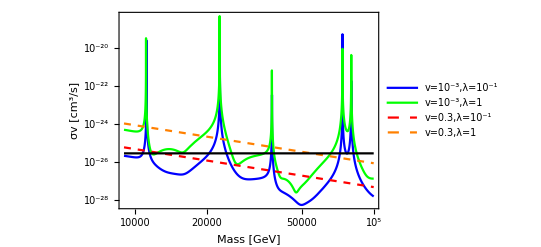

```mathematica
LogLogPlot[{Evaluate[Abs[σv[M,10^-1]]],Evaluate[Abs[σv[M,1]]], Evaluate[Abs[f[M,10^-1]]],Evaluate[Abs[f[M,1]]],3*10^-26},{M,9000,100000},PlotStyle->{Directive[Blue,Thick],Directive[Green,Thick],Directive[Red,Dashed,Thick],Directive[Orange,Dashed,Thick],Directive[Black,Thick]},Frame-> True,FrameStyle-> Directive[Black,26],PlotLegends->{"v=10^-3,λ=10^-1 ","v=10^-3,λ=1","v=0.3,λ=10^-1","v=0.3,λ=1"},FrameLabel->{Style["Mass [GeV]",26],Style["σv [cm^3/s]",26]},RotateLabel-> False,PlotRange->All]
```

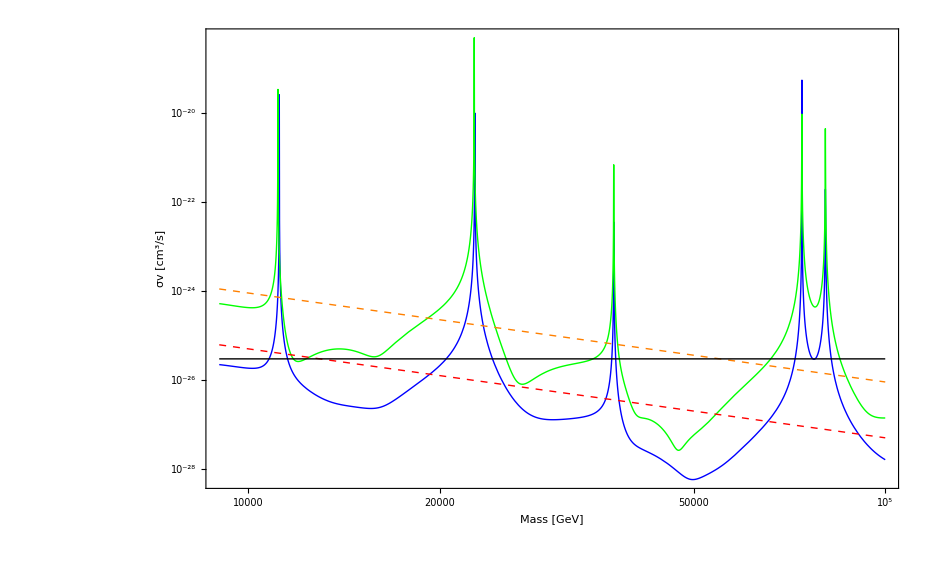

```mathematica
Show[%24,PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
data=Parallelize[Table[{M,Abs[σv[M,10^-1]],Abs[σv[M,1]],Abs[f[M,10^-1]],Abs[f[M,1]],N[3*10^-26]},{M,96001,100000}]];
```

```mathematica
Export["quint.csv",data];(*Exportar los datos a un archivo CSV*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["quint.csv"]]]
```